# A Rayleigh criterion for mechanical instability: inducing activity by chemo–mechanical coupling

## The Markov jump process

## The generator

```mathematica
states={a,b,c};
n=Length[states];

(*Potential energy states*)
En[a]=λ*U[x,a];
En[b]=λ*U[x,b];
En[c]=λ*U[x,c];

(*Driving factor W(i,j)—antisymmetric*)
W[a,b]=w;
W[b,c]=w;
W[c,a]=w;
W[i_,j_]:=-W[j,i];  (*Antisymmetry rule*)
W[i_,j_]:=0/;i===j;

(*Transition rate function*)
k[i_,j_]:=ψ[i,j]*Exp[β/2*(En[i]-En[j]+W[i,j])];

(*Generator*)
Q=ConstantArray[0,{n,n}];
Do[Q[[i,j]]=k[states[[i]],states[[j]]]/.{er->0,er2->0},{i,n},{j,n}];
(*Set diagonal elements*)
Do[Q[[i,i]]=-Total[Delete[Q[[i]],i]],{i,n}];
Q=Q/.{ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]};
MatrixForm[Q]
```

(-ⅇ^(1/2 β (w+λ U[x,a]-λ U[x,b])) ψ[a,b]-ⅇ^(1/2 β (-w+λ U[x,a]-λ U[x,c])) ψ[c,a] | ⅇ^(1/2 β (w+λ U[x,a]-λ U[x,b])) ψ[a,b] | ⅇ^(1/2 β (-w+λ U[x,a]-λ U[x,c])) ψ[c,a]
ⅇ^(1/2 β (-w-λ U[x,a]+λ U[x,b])) ψ[a,b] | -ⅇ^(1/2 β (-w-λ U[x,a]+λ U[x,b])) ψ[a,b]-ⅇ^(1/2 β (w+λ U[x,b]-λ U[x,c])) ψ[b,c] | ⅇ^(1/2 β (w+λ U[x,b]-λ U[x,c])) ψ[b,c]
ⅇ^(1/2 β (w-λ U[x,a]+λ U[x,c])) ψ[c,a] | ⅇ^(1/2 β (-w-λ U[x,b]+λ U[x,c])) ψ[b,c] | -ⅇ^(1/2 β (-w-λ U[x,b]+λ U[x,c])) ψ[b,c]-ⅇ^(1/2 β (w-λ U[x,a]+λ U[x,c])) ψ[c,a])

## Total equilibrium distribution (ρ^eq)_tot(x,v,σ)

```mathematica
Energy[x_,v_,σ_]=m*v^2/2+V[x]+λ*U[x,σ];
ρeqtot=Exp[-β*Energy[x,v,σ]];
```

```mathematica
-v*D[ρeqtot,x]+1/m*(D[V[x],x]+λ*D[U[x,σ],x])*D[ρeqtot,v]
```

0

```mathematica
FullSimplify[Sum[k[states[[1]],states[[j]]]*(ρeqtot/.{σ->states[[1]]})-k[states[[j]],states[[1]]]*(ρeqtot/.{σ->states[[j]]}), {j,n}]]/.{w->0,ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]}
FullSimplify[Sum[k[states[[2]],states[[j]]]*(ρeqtot/.{σ->states[[2]]})-k[states[[j]],states[[2]]]*(ρeqtot/.{σ->states[[j]]}), {j,n}]]/.{w->0,ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]}
FullSimplify[Sum[k[states[[3]],states[[j]]]*(ρeqtot/.{σ->states[[3]]})-k[states[[j]],states[[3]]]*(ρeqtot/.{σ->states[[j]]}), {j,n}]]/.{w->0,ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]}
```

0

0

0

## Born-Oppenheimer distribution ρ_x(σ)

### The solution

```mathematica
ρ={f,g,h};
Qtrans=Transpose[Q];
sol=Simplify[Solve[Qtrans.ρ==0,{g,h}],{β>0,w>0,ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]}];
ρs=ρ/.{sol[[1,2]],sol[[1,1]]};
normalisation=Solve[Total[ρs]==1,f];
ρf=FullSimplify[ρs/.{f->normalisation[[1,1,2]]},{β>0,w>0,ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]}]
FullSimplify[Qtrans.ρf]
FullSimplify[Total[ρf]]
```

{(ⅇ^(1/2 β (4 w+λ (U[x,a]+U[x,b]))) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β λ (U[x,a]+U[x,c])) ψ[b,c]+ⅇ^(w β+1/2 β λ (U[x,b]+U[x,c])) ψ[c,a]))/((ⅇ^(1/2 β λ (3 U[x,a]-U[x,b]))+ⅇ^(1/2 β (4 w+λ (U[x,a]+U[x,b])))+ⅇ^(w β+1/2 β λ (3 U[x,a]+U[x,b]-2 U[x,c]))) ψ[b,c] ψ[c,a]+ψ[a,b] ((ⅇ^(1/2 β λ (U[x,a]+U[x,c]))+ⅇ^(1/2 β (4 w+3 λ U[x,a]-λ U[x,c]))+ⅇ^(w β+1/2 β λ (3 U[x,a]-2 U[x,b]+U[x,c]))) ψ[b,c]+(ⅇ^(1/2 β λ (2 U[x,a]+U[x,b]-U[x,c]))+ⅇ^(1/2 β (4 w+λ (2 U[x,a]-U[x,b]+U[x,c])))+ⅇ^(w β+1/2 β λ (U[x,b]+U[x,c]))) ψ[c,a])),(ⅇ^(β λ U[x,a]+3/2 β λ U[x,c]) (ⅇ^(1/2 β λ (U[x,a]+U[x,b]-U[x,c])) ψ[b,c] ψ[c,a]+ⅇ^(w β) ψ[a,b] (ⅇ^(1/2 β λ U[x,a]) ψ[b,c]+ⅇ^(w β+1/2 β λ U[x,b]) ψ[c,a])))/((ⅇ^(w β+3/2 β λ (U[x,a]+U[x,b]))+ⅇ^(1/2 β λ (3 U[x,a]+U[x,b]+2 U[x,c]))+ⅇ^(1/2 β (4 w+λ (U[x,a]+3 U[x,b]+2 U[x,c])))) ψ[b,c] ψ[c,a]+ψ[a,b] ((ⅇ^(1/2 β λ (U[x,a]+2 U[x,b]+3 U[x,c]))+ⅇ^(w β+3/2 β λ (U[x,a]+U[x,c]))+ⅇ^(1/2 β (4 w+λ (3 U[x,a]+2 U[x,b]+U[x,c])))) ψ[b,c]+(ⅇ^(1/2 β λ (2 U[x,a]+3 U[x,b]+U[x,c]))+ⅇ^(w β+3/2 β λ (U[x,b]+U[x,c]))+ⅇ^(1/2 β (4 w+λ (2 U[x,a]+U[x,b]+3 U[x,c])))) ψ[c,a])),(ⅇ^(1/2 β λ (2 U[x,a]+3 U[x,b]+U[x,c])) (ⅇ^(1/2 β (2 w+λ U[x,a]-λ U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β (4 w+λ U[x,a]-λ U[x,b])) ψ[b,c]+ψ[c,a])))/((ⅇ^(w β+3/2 β λ (U[x,a]+U[x,b]))+ⅇ^(1/2 β λ (3 U[x,a]+U[x,b]+2 U[x,c]))+ⅇ^(1/2 β (4 w+λ (U[x,a]+3 U[x,b]+2 U[x,c])))) ψ[b,c] ψ[c,a]+ψ[a,b] ((ⅇ^(1/2 β λ (U[x,a]+2 U[x,b]+3 U[x,c]))+ⅇ^(w β+3/2 β λ (U[x,a]+U[x,c]))+ⅇ^(1/2 β (4 w+λ (3 U[x,a]+2 U[x,b]+U[x,c])))) ψ[b,c]+(ⅇ^(1/2 β λ (2 U[x,a]+3 U[x,b]+U[x,c]))+ⅇ^(w β+3/2 β λ (U[x,b]+U[x,c]))+ⅇ^(1/2 β (4 w+λ (2 U[x,a]+U[x,b]+3 U[x,c])))) ψ[c,a]))}

{0,0,0}

1

```mathematica
stateMap=<|a->1,b->2,c->3|>;
delta[σ_,σ0_]:=KroneckerDelta[stateMap[σ],stateMap[σ0]]
Π[σ_]:=Switch[σ,a,b,b,c,c,a,_,σ  (*default:return eta unchanged*)]
vec[σ0_]:=Table[delta[σ,σ0],{σ,states}]
ρs2[σ_]:=(ψ[Π[σ],σ]*ψ[Π[Π[σ]],σ]*Exp[β*λ/2*(U[x,Π[σ]]+U[x, Π[Π[σ]]]-2*U[x,σ])]+ψ[Π[σ],σ]*ψ[Π[Π[σ]],Π[σ]]*Exp[β*λ/2*(U[x, Π[Π[σ]]]-U[x,σ])]*Exp[-β*w]+ψ[Π[σ],Π[Π[σ]]]*ψ[Π[Π[σ]],σ]*Exp[β*λ/2*(U[x,Π[σ]]-U[x,σ])]*Exp[β*w])/.{ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]};
norm = (ρs2[a]+ρs2[b]+ρs2[c])/.{ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]};
ρf2[σ_]:=(ψ[Π[σ],σ]*ψ[Π[Π[σ]],σ]*Exp[β*λ/2*(U[x,Π[σ]]+U[x, Π[Π[σ]]]-2*U[x,σ])]+ψ[Π[σ],σ]*ψ[Π[Π[σ]],Π[σ]]*Exp[β*λ/2*(U[x, Π[Π[σ]]]-U[x,σ])]*Exp[-β*w]+ψ[Π[σ],Π[Π[σ]]]*ψ[Π[Π[σ]],σ]*Exp[β*λ/2*(U[x,Π[σ]]-U[x,σ])]*Exp[β*w])/norm/.{ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]};
FullSimplify[ρf[[1]]-ρf2[a]]
FullSimplify[ρf[[2]]-ρf2[b]]
FullSimplify[ρf[[3]]-ρf2[c]]
```

0

0

0

### Small couplig limit

```mathematica
h[σ_]:=(β/2*(U[x,Π[σ]]+U[x,Π[Π[σ]]])+Ψ[Π[σ],σ]+Ψ[Π[Π[σ]],σ]+(β/2*(U[x,σ]+U[x,Π[Π[σ]]])+Ψ[Π[σ],σ]+Ψ[Π[Π[σ]],Π[σ]])*Exp[-β*w]+(β/2*(U[x,Π[σ]]+U[x,σ])+Ψ[Π[σ],Π[Π[σ]]]+Ψ[Π[Π[σ]],σ])*Exp[β*w])/.{Ψ[b,a]->Ψ[a,b], Ψ[c,b]->Ψ[b,c], Ψ[a,c]->Ψ[c,a]}
ρsmallc[σ_]:=1/3*(1+λ*(-2 /3(Ψ[a,b]+Ψ[b,c]+Ψ[c,a])+1/(1+2*Cosh[β*w])*h[σ]-β*U[x,σ]))
```

```mathematica
ρfliml=FullSimplify[Normal[Series[FullSimplify[ρf/.{ψ[c,a]->Subscript[ψ, 0]*(1+λ*Ψ[c,a]),ψ[b,c]->Subscript[ψ, 0]*(1+λ*Ψ[b,c]),ψ[a,b]->Subscript[ψ, 0]*(1+λ*Ψ[a,b])}],{λ,0,1}]]]
FullSimplify[ρsmallc[a]-ρfliml[[1]]]
FullSimplify[ρsmallc[b]-ρfliml[[2]]]
FullSimplify[ρsmallc[c]-ρfliml[[3]]]
```

{1/9 (3-λ (3 β U[x,a]+2 (Ψ[a,b]+Ψ[b,c]+Ψ[c,a]))+(3 λ (β (U[x,a]+U[x,c])+2 (Ψ[a,b]+Ψ[b,c])+ⅇ^(w β) (β (U[x,b]+U[x,c])+2 (Ψ[a,b]+Ψ[c,a]))+ⅇ^(2 w β) (β (U[x,a]+U[x,b])+2 (Ψ[b,c]+Ψ[c,a]))))/(2 (1+ⅇ^(w β)+ⅇ^(2 w β)))),1/18 (6-3 β λ U[x,b]+3 β λ U[x,c]+2 λ Ψ[a,b]-4 λ Ψ[b,c]+(3 λ (β U[x,a]-β U[x,c]-2 Ψ[a,b]+2 Ψ[b,c]+ⅇ^(w β) (β U[x,a]-β U[x,b]+2 Ψ[b,c]-2 Ψ[c,a])))/(1+ⅇ^(w β)+ⅇ^(2 w β))+2 λ Ψ[c,a]),1/18 (6+3 β λ U[x,a]-3 β λ U[x,c]+2 λ Ψ[a,b]+2 λ Ψ[b,c]-4 λ Ψ[c,a]+(3 λ (-β U[x,a]+β U[x,b]-2 Ψ[b,c]+2 Ψ[c,a]+ⅇ^(w β) (β U[x,b]-β U[x,c]-2 Ψ[a,b]+2 Ψ[c,a])))/(1+ⅇ^(w β)+ⅇ^(2 w β)))}

0

0

0

```mathematica
Normal[Series[FullSimplify[ρf[[1]]/.{U[x,b]->0,U[x,c]->0,ψ[c,a]->Subscript[ψ, 0],ψ[b,c]->Subscript[ψ, 0],ψ[a,b]->Subscript[ψ, 0]*(1+λ*Ψ[x])}],{λ,0,1}]]
```

1/3+λ (1/9 (-3 β U[x,a]-2 Ψ[x])+(1/2 β U[x,a]+1/2 ⅇ^(2 w β) β U[x,a]+(1+ⅇ^(w β)) Ψ[x])/(3 (1+ⅇ^(w β)+ⅇ^(2 w β))))

```mathematica
FullSimplify[1/9 (-3 β U[x,a]-2 Ψ[x])+(1/2 β U[x,a]+1/2 ⅇ^(2 w β) β U[x,a]+(1+ⅇ^(w β)) Ψ[x])/(3 (1+ⅇ^(w β)+ⅇ^(2 w β)))]
```

-(3 β (1+Cosh[w β]) U[x,a]+(-1+Cosh[w β]+3 Sinh[w β]) Ψ[x])/(9+18 Cosh[w β])

### Large driving limit

```mathematica
ρlimw=FullSimplify[Limit[ρf,w->Infinity],{β>0,w>0,λ>0,U[x,a] ∈Reals,U[x,b] ∈Reals,U[x,c] ∈Reals,ψ[a,b]∈Reals,ψ[b,c]∈Reals,ψ[c,a]∈Reals}]
ρlargew[σ_]:=Exp[β*λ/2*(U[x,Π[σ]]-U[x,σ])]/ψ[σ,Π[σ]]/(Exp[β*λ/2*(U[x,Π[a]]-U[x,a])]/ψ[a,Π[a]]+Exp[β*λ/2*(U[x,Π[b]]-U[x,b])]/ψ[b,Π[b]]+Exp[β*λ/2*(U[x,Π[c]]-U[x,c])]/ψ[c,Π[c]])
FullSimplify[ρlimw[[1]]-ρlargew[a]]
FullSimplify[ρlimw[[2]]-ρlargew[b]]
FullSimplify[ρlimw[[3]]-ρlargew[c]]
```

{(ⅇ^(1/2 β λ (2 U[x,b]+U[x,c])) ψ[b,c] ψ[c,a])/(ⅇ^(1/2 β λ (2 U[x,b]+U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β λ (2 U[x,a]+U[x,b])) ψ[b,c]+ⅇ^(1/2 β λ (U[x,a]+2 U[x,c])) ψ[c,a])),(ⅇ^(1/2 β λ (U[x,a]+2 U[x,c])) ψ[a,b] ψ[c,a])/(ⅇ^(1/2 β λ (2 U[x,b]+U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β λ (2 U[x,a]+U[x,b])) ψ[b,c]+ⅇ^(1/2 β λ (U[x,a]+2 U[x,c])) ψ[c,a])),(ψ[a,b] ψ[b,c])/(ⅇ^(1/2 β λ (-2 U[x,a]+U[x,b]+U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ψ[b,c]+ⅇ^(-1/2 β λ (U[x,a]+U[x,b]-2 U[x,c])) ψ[c,a]))}

0

0

0

```mathematica
ρlimw2=FullSimplify[Limit[ρf,w->-Infinity],{β>0,w>0,λ>0,U[x,a] ∈Reals,U[x,b] ∈Reals,U[x,c] ∈Reals,ψ[a,b]∈Reals,ψ[b,c]∈Reals,ψ[c,a]∈Reals}]
ρlargew2[σ_]:=Exp[β*λ/2*(U[x,Π[Π[σ]]]-U[x,σ])]/ψ[Π[Π[σ]],σ]/(Exp[β*λ/2*(U[x,Π[Π[a]]]-U[x,a])]/ψ[a,Π[Π[a]]]+Exp[β*λ/2*(U[x,Π[Π[b]]]-U[x,b])]/ψ[b,Π[Π[b]]]+Exp[β*λ/2*(U[x,Π[Π[c]]]-U[x,c])]/ψ[c,Π[Π[c]]])/.{ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]}
FullSimplify[ρlimw2[[1]]-ρlargew2[a]]
FullSimplify[ρlimw2[[2]]-ρlargew2[b]]
FullSimplify[ρlimw2[[3]]-ρlargew2[c]]
```

{(ⅇ^(1/2 β λ (U[x,b]+2 U[x,c])) ψ[a,b] ψ[b,c])/(ⅇ^(1/2 β λ (2 U[x,a]+U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β λ (U[x,b]+2 U[x,c])) ψ[b,c]+ⅇ^(1/2 β λ (U[x,a]+2 U[x,b])) ψ[c,a])),(ⅇ^(1/2 β λ (2 U[x,a]+U[x,c])) ψ[b,c] ψ[c,a])/(ⅇ^(1/2 β λ (2 U[x,a]+U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β λ (U[x,b]+2 U[x,c])) ψ[b,c]+ⅇ^(1/2 β λ (U[x,a]+2 U[x,b])) ψ[c,a])),(ⅇ^(1/2 β λ (U[x,a]+2 U[x,b])) ψ[a,b] ψ[c,a])/(ⅇ^(1/2 β λ (2 U[x,a]+U[x,c])) ψ[b,c] ψ[c,a]+ψ[a,b] (ⅇ^(1/2 β λ (U[x,b]+2 U[x,c])) ψ[b,c]+ⅇ^(1/2 β λ (U[x,a]+2 U[x,b])) ψ[c,a]))}

0

0

0

## Equilibruim Born-Oppenheimer distribution ρ_x^eq(σ)

```mathematica
ρeq=ConstantArray[0,n];
Zx=Exp[-β*λ*U[x,a]]+Exp[-β*λ*U[x,b]]+Exp[-β*λ*U[x,c]];
Do[ρeq[[i]]=Exp[-β*En[states[[i]]]]/Zx,{i,n}];
ρeq
FullSimplify[Total[ρeq]]
DB=ConstantArray[0,{n,n}];
Do[DB[[i,j]]=(k[states[[i]],states[[j]]]*ρeq[[i]]-k[states[[j]],states[[i]]]*ρeq[[j]])/.{w->0,ψ[b,a]->ψ[a,b], ψ[c,b]->ψ[b,c], ψ[a,c]->ψ[c,a]},{i,n},{j,n}];
FullSimplify[DB]
```

{ⅇ^(-β λ U[x,a])/(ⅇ^(-β λ U[x,a])+ⅇ^(-β λ U[x,b])+ⅇ^(-β λ U[x,c])),ⅇ^(-β λ U[x,b])/(ⅇ^(-β λ U[x,a])+ⅇ^(-β λ U[x,b])+ⅇ^(-β λ U[x,c])),ⅇ^(-β λ U[x,c])/(ⅇ^(-β λ U[x,a])+ⅇ^(-β λ U[x,b])+ⅇ^(-β λ U[x,c]))}

1

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
ρeq2=FullSimplify[ρf/.{w->0}]
FullSimplify[ρeq-ρeq2]
```

{ⅇ^(β λ (U[x,b]+U[x,c]))/(ⅇ^(β λ (U[x,a]+U[x,b]))+ⅇ^(β λ (U[x,a]+U[x,c]))+ⅇ^(β λ (U[x,b]+U[x,c]))),ⅇ^(β λ (U[x,a]+U[x,c]))/(ⅇ^(β λ (U[x,a]+U[x,b]))+ⅇ^(β λ (U[x,a]+U[x,c]))+ⅇ^(β λ (U[x,b]+U[x,c]))),ⅇ^(β λ (U[x,a]+U[x,b]))/(ⅇ^(β λ (U[x,a]+U[x,b]))+ⅇ^(β λ (U[x,a]+U[x,c]))+ⅇ^(β λ (U[x,b]+U[x,c])))}

{0,0,0}

## Distribution ρ_x(σ,t)

### Full result

```mathematica
Qexpb=MatrixExp[Transpose[Q]*τ];
ρt[σ0_]:=Qexpb.vec[σ0]
M=Transpose[{ρt[a],ρt[b],ρt[c]}]
```

```mathematica
(* Specific components *)
ρtaasmallc=FullSimplify[Simplify[ρt[a][[1]]/.{U[x,b]->0,U[x,c]->0,ψ[b,c]->Subscript[ψ, 0], ψ[c,a]->Subscript[ψ, 0],ψ[a,b]->Subscript[ψ, 0],U[x,a]->U[x],λ->0},{Subscript[ψ, 0]>0,β>0}],{β>0,w ∈Reals}]
```

1/3 (1+2 ⅇ^(-3 τ Cosh[(w β)/2] ψ_0) Cos[√3 τ Sinh[(w β)/2] ψ_0])

```mathematica
FullSimplify[Integrate[ρtaasmallc-1/3,{τ,0,Infinity}],{Subscript[ψ, 0]>0,β>0,w ∈Reals}]
```

(2 Cosh[(w β)/2])/(3 ψ_0+6 Cosh[w β] ψ_0)

```mathematica
ρtbasmallc=FullSimplify[Simplify[ρt[b][[1]]/.{U[x,b]->0,U[x,c]->0,ψ[b,c]->Subscript[ψ, 0], ψ[c,a]->Subscript[ψ, 0],ψ[a,b]->Subscript[ψ, 0],U[x,a]->U[x],λ->0},{Subscript[ψ, 0]>0,β>0}],{β>0,w ∈Reals}]
```

1/3-1/3 ⅇ^(-3 τ Cosh[(w β)/2] ψ_0) (Cos[√3 τ Sinh[(w β)/2] ψ_0]+√3 Sin[√3 τ Sinh[(w β)/2] ψ_0])

```mathematica
ρtcasmallc=FullSimplify[Simplify[ρt[c][[1]]/.{U[x,b]->0,U[x,c]->0,ψ[b,c]->Subscript[ψ, 0], ψ[c,a]->Subscript[ψ, 0],ψ[a,b]->Subscript[ψ, 0],U[x,a]->U[x],λ->0},{Subscript[ψ, 0]>0,β>0}],{β>0,w ∈Reals}]
```

1/3 (1+ⅇ^(-3 τ Cosh[(w β)/2] ψ_0) (-Cos[√3 τ Sinh[(w β)/2] ψ_0]+√3 Sin[√3 τ Sinh[(w β)/2] ψ_0]))

```mathematica
FullSimplify[Integrate[FullSimplify[-ρtaasmallc*2*(1+Cosh[β*w])+ρtbasmallc*(1+Exp[-β*w])+ρtcasmallc*(1+Exp[β*w])],{τ,0,Infinity}],{β>0,w ∈Reals,Subscript[ψ, 0]>0}]
```

-(4 Cosh[(w β)/2] (2+Cosh[w β]))/(3 (1+2 Cosh[w β]) ψ_0)

```mathematica
FullSimplify[Integrate[FullSimplify[ρtaasmallc*(1-Cosh[β*w]-3*Sinh[β*w])+ρtbasmallc*(1-Cosh[β*w]+3*Sinh[β*w])+ρtcasmallc*2*(Cosh[β*w]-1)],{τ,0,Infinity}],{β>0,w ∈Reals,Subscript[ψ, 0]>0}]
```

(ⅇ^((w β)/2) (-1+Cosh[w β]-3 Sinh[w β]))/((1+2 Cosh[w β]) ψ_0)

```mathematica
FullSimplify[(ⅇ^((w β)/2) (-1+Cosh[w β]-3 Sinh[w β]))/((1+2 Cosh[w β]) Subscript[ψ, 0])-(-(Exp[-β*w/2]/((1+2 Cosh[w β]) Subscript[ψ, 0])*(Exp[2*β*w]+Exp[β*w]-2)))]
```

0

### Large driving analysis

```mathematica
Qw = FullSimplify[(Q/.{U[x,b]->0,U[x,c]->0,ψ[b,c]->Subscript[ψ, 0],ψ[c,a]->Subscript[ψ, 0],ψ[a,b]->Subscript[ψ, 0]*Ψ[a,b]})/(Subscript[ψ, 0]*Exp[β*w/2])]
```

{{-ⅇ^(-w β+1/2 β λ U[x,a]) (1+ⅇ^(w β) Ψ[a,b]),ⅇ^(1/2 β λ U[x,a]) Ψ[a,b],ⅇ^(-w β+1/2 β λ U[x,a])},{ⅇ^(-1/2 β (2 w+λ U[x,a])) Ψ[a,b],-1-ⅇ^(-1/2 β (2 w+λ U[x,a])) Ψ[a,b],1},{ⅇ^(-1/2 β λ U[x,a]),ⅇ^(-w β),-ⅇ^(-w β)-ⅇ^(-1/2 β λ U[x,a])}}

```mathematica
FullSimplify[Limit[Qw,w->Infinity],{β>0,λ∈Reals,U[x,a] ∈Reals,Ψ[a,b]∈Reals}]
```

{{-ⅇ^(1/2 β λ U[x,a]) Ψ[a,b],ⅇ^(1/2 β λ U[x,a]) Ψ[a,b],0},{0,-1,1},{ⅇ^(-1/2 β λ U[x,a]),0,-ⅇ^(-1/2 β λ U[x,a])}}

## Reduced dynamics

## Noise coefficient Β

### Full Result

```mathematica
dU={Derivative[1,0][U][x,a],Derivative[1,0][U][x,b],Derivative[1,0][U][x,c]};
dUρ={D[U[x,a],x]*ρf[[1]], D[U[x,b],x]*ρf[[2]], D[U[x,c], x]*ρf[[3]]};
Bint=λ^2*(dU.M.dUρ-(dU.ρf)^2)
```

### Plotting full result

```mathematica
ua[x_]=U0*Cos[2*π*x/L]
```

U0 Cos[(2 π x)/L]

```mathematica
Bintscaled[y_,l_,u0_,Ψ0_,ϕ_,W_]=100*L^2*β^2((Bint/.{U[x,a]->ua[x],U[x,b]->0,U[x,c]->0, ψ[b,c]->ψ0,ψ[c,a]->ψ0,ψ[a,b]->ψ0*(1+λ*Ψ0*Cos[2*π*x/L+ϕ]),w->W/β,Derivative[1,0][U][x,b]->0,Derivative[1,0][U][x,c]->0,Derivative[1,0][U][x,a]->D[ua[x],x]})/.{x->y*L,U0->u0/β,τ->s/ψ0})/.{λ->l}
```

```mathematica
dataw0=Table[{i,NIntegrate[Simplify[Bintscaled[i,1/Sqrt[100],0.5,5,π,0.000001],ψ0>0],{s,0,Infinity}]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataw1=Table[{i,NIntegrate[Simplify[Bintscaled[i,1/Sqrt[100],0.5,5,π,1],ψ0>0],{s,0,Infinity}]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataw3=Table[{i,NIntegrate[Simplify[Bintscaled[i,1/Sqrt[100],0.5,5,π,3],ψ0>0],{s,0,Infinity}]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataw5=Table[{i,NIntegrate[Simplify[Bintscaled[i,1/Sqrt[100],0.5,5,π,5],ψ0>0],{s,0,Infinity}]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataw8=Table[{i,NIntegrate[Simplify[Bintscaled[i,1/Sqrt[100],0.5,5,π,8],ψ0>0],{s,0,Infinity}]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

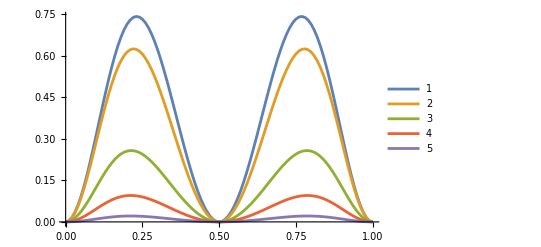

```mathematica
ListPlot[{dataw0,dataw1,dataw3,dataw5,dataw8},Joined->True,PlotLegends->Automatic]
```

### Perturbative result

```mathematica
Ψa=Subscript[ψ, 0]*(1+λ*Ψ[x]);
Ψb=Subscript[ψ, 0]*(1+λ*ϕ[x]);
Ψc=Subscript[ψ, 0]*(1+λ*Φ[x]);
ρper=Simplify[ρf/.{ψ[a,b]->Ψa,ψ[b,c]->Ψb,ψ[c,a]->Ψc}];
Qper=Q/.{ψ[a,b]->Ψa,ψ[b,c]->Ψb,ψ[c,a]->Ψc};
Qexpper=MatrixExp[Transpose[Qper]*τ];
ρtper[σ0_]:=Qexpper.vec[σ0];
Mper=Transpose[{ρtper[a],ρtper[b],ρtper[c]}];
dUρper={D[U[x,a],x]*ρper[[1]], D[U[x,b],x]*ρper[[2]], D[U[x,c], x]*ρper[[3]]};
Bintper=λ^2*FullSimplify[(dU.Mper.dUρper-(dU.ρper)^2)/.{λ->0}]
```

1/9 ⅇ^(-1/2 ⅇ^(-w β) (√3 √(-ⅇ^(w β) (-1+ⅇ^(w β))^2)+3 ⅇ^((w β)/2) (1+ⅇ^(w β))) τ ψ_0) (1+ⅇ^(√3 ⅇ^(-w β) √(-ⅇ^(w β) (-1+ⅇ^(w β))^2) τ ψ_0)) λ^2 ((U^(1,0)[x,a])^2+(U^(1,0)[x,b])^2-U^(1,0)[x,b] U^(1,0)[x,c]+(U^(1,0)[x,c])^2-U^(1,0)[x,a] (U^(1,0)[x,b]+U^(1,0)[x,c]))

```mathematica
Bper=FullSimplify[Integrate[Bintper,{τ,0,Infinity}],{β>0,λ>0,w ∈Reals,β∈Reals,Subscript[ψ, 0]>0}]
```

(2 λ^2 Cosh[(w β)/2] ((U^(1,0)[x,a])^2+(U^(1,0)[x,b])^2-U^(1,0)[x,b] U^(1,0)[x,c]+(U^(1,0)[x,c])^2-U^(1,0)[x,a] (U^(1,0)[x,b]+U^(1,0)[x,c])))/(9 (ψ_0+2 Cosh[w β] ψ_0))

## Friction coefficient ν

### Full result

```mathematica
Qexpb2=MatrixExp[(Transpose[Q]/.{ψ[b,c]->ψ[b,c,x],ψ[c,a]->ψ[c,a,x],ψ[a,b]->ψ[a,b,x]})*τ];
ρt2[σ0_]:=Qexpb2.vec[σ0]
M2=Transpose[{ρt2[a],ρt2[b],ρt2[c]}];
dρ=Simplify[D[(ρf/.{ψ[b,c]->ψ[b,c,x],ψ[c,a]->ψ[c,a,x],ψ[a,b]->ψ[a,b,x]}),x]];
νint=-λ*dU.(M2.dρ)
```

```mathematica
ua[x_]=U0 Cos[(2 π x)/L]
```

U0 Cos[(2 π x)/L]

```mathematica
νintscaled[y_,l_,u0_,Ψ0_,ϕ_,W_]=100*β*L^2(((νint/.{U[x,a]->ua[x],U[x,b]->0,U[x,c]->0, ψ[b,c,x]->ψ0,ψ[c,a,x]->ψ0,ψ[a,b,x]->ψ0*(1+λ*Ψ0*Cos[2*π*x/L+ϕ]),Derivative[0,0,1][ψ][b,c,x]->0,Derivative[0,0,1][ψ][c,a,x]->0,Derivative[0,0,1][ψ][a,b,x]->D[ψ0*(1+λ*Ψ0*Cos[2*π*x/L+ϕ]),x],w->W/β,Derivative[1,0][U][x,b]->0,Derivative[1,0][U][x,c]->0,Derivative[1,0][U][x,a]->D[ua[x],x]})/.{λ->l,x->y*L,U0->u0/β,τ->s/ψ0}))
```

```mathematica
dataνw0=Table[{i,Re[NIntegrate[Simplify[νintscaled[i,1/Sqrt[100],0.5,5,π,0.00001],ψ0>0],{s,0,Infinity}]]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataνw1=Table[{i,Re[NIntegrate[Simplify[νintscaled[i,1/Sqrt[100],0.5,5,π,1],ψ0>0],{s,0,Infinity}]]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataνw3=Table[{i,Re[NIntegrate[Simplify[νintscaled[i,1/Sqrt[100],0.5,5,π,3],ψ0>0],{s,0,Infinity}]]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataνw5=Table[{i,Re[NIntegrate[Simplify[νintscaled[i,1/Sqrt[100],0.5,5,π,5],ψ0>0],{s,0,Infinity}]]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dataνw8=Table[{i,Re[NIntegrate[Simplify[νintscaled[i,1/Sqrt[100],0.5,5,π,8],ψ0>0],{s,0,Infinity}]]},{i,0,1,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

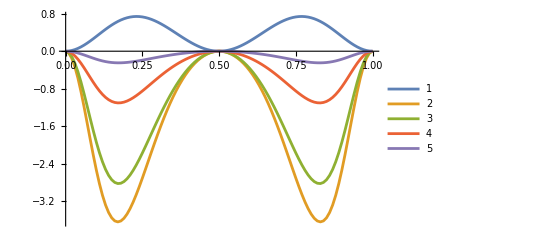

```mathematica
ListPlot[{dataνw0,dataνw1,dataνw3,dataνw5,dataνw8},Joined->True,PlotLegends->Automatic]
```

### Perturbative result

```mathematica
dρper=FullSimplify[Normal[Series[D[ρper,x],{λ,0,1}]],{β>0,λ>0,w>0,w ∈Reals,β∈Reals}];
νintper=λ*Simplify[-dU.(Mper/.{λ->0}).dρper,{β>0,λ>0,w>0,w ∈Reals,β∈Reals}];
νper=Simplify[Integrate[νintper,{τ,0,Infinity}],{β>0,λ>0,w>0,w ∈Reals,β∈Reals,Subscript[ψ, 0]>0}];
FullSimplify[νper/.{ϕ'[x]->0,Φ'[x]->0,Derivative[1,0][U][x,b]->0,Derivative[1,0][U][x,c]->0}]
```

(ⅇ^(2 w β) λ^2 U^(1,0)[x,a] (ⅇ^(-(w β)/2) (-2+ⅇ^(w β)+ⅇ^(2 w β)) Ψ'[x]+β (5 Cosh[(w β)/2]+Cosh[(3 w β)/2]) U^(1,0)[x,a]))/(9 (1+ⅇ^(w β)+ⅇ^(2 w β))^2 ψ_0)

```mathematica
FullSimplify[Limit[(νper/Bper),w->0]]
νper1=FullSimplify[νper/.{Ψ'[x]->0, ϕ'[x]->0,Φ'[x]->0}]
γper=FullSimplify[νper-νper1]
FullSimplify[γper/.{ϕ'[x]->0,Φ'[x]->0,Derivative[1,0][U][x,b]->0,Derivative[1,0][U][x,c]->0}]
```

β

(β λ^2 (5 Cosh[(w β)/2]+Cosh[(3 w β)/2]) ((U^(1,0)[x,a])^2+(U^(1,0)[x,b])^2-U^(1,0)[x,b] U^(1,0)[x,c]+(U^(1,0)[x,c])^2-U^(1,0)[x,a] (U^(1,0)[x,b]+U^(1,0)[x,c])))/(9 (1+2 Cosh[w β])^2 ψ_0)

1/(9 (1+2 Cosh[w β])^2 ψ_0)2 λ^2 Sinh[(w β)/2] (ϕ'[x] (-2 Sinh[w β] U^(1,0)[x,a]+(2+ⅇ^(w β)) U^(1,0)[x,b]+(-2-ⅇ^(-w β)) U^(1,0)[x,c])+Φ'[x] ((-2-ⅇ^(-w β)) U^(1,0)[x,a]-2 Sinh[w β] U^(1,0)[x,b]+(2+ⅇ^(w β)) U^(1,0)[x,c])+Ψ'[x] ((2+ⅇ^(w β)) U^(1,0)[x,a]+(-2-ⅇ^(-w β)) U^(1,0)[x,b]-2 Sinh[w β] U^(1,0)[x,c]))

(2 (2+ⅇ^(w β)) λ^2 Sinh[(w β)/2] Ψ'[x] U^(1,0)[x,a])/(9 (1+2 Cosh[w β])^2 ψ_0)